```mathematica
位于原点的正电荷的电力线分布——直接计算
```

(y(x))/x

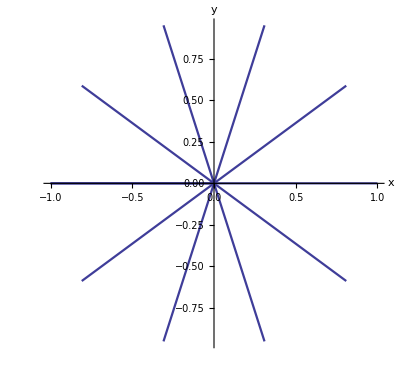

```mathematica
ϕ[x_,y_]:=1/√(x^2+y^2);
Ex=-D[ϕ[x,y],x];Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x]
r=10.0^-3;R=1.0;forceline={};
equ={y'[x]==k,y[xstart]==ystart};
Do[
xstart=r*Cos[θ];ystart=r*Sin[θ];
xend=R*Cos[θ];
s=NDSolve[equ,y,{x,xstart,xend}];
y=y/.s[[1]];
figure=Plot[y[x],{x,xstart,xend},
AspectRatio->Automatic,
PlotStyle->Thickness[0.004]];
AppendTo[forceline,figure];Clear[y],
{θ,-π,π,π/5.0}]
Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"},
BaseStyle->{FontSize->12}]
Clear[ϕ,forceline,xstart,ystart,xend,y]
```